```mathematica
Geräteliste
```

Micrometerschraube	U=0.01mm

pro stab 5 gewichte
alu	5-75g
sta	50-250g
mes	100-1500g

## 1.

### Abmessungen Stab

1. alu 2. mes 3. sta in mm mit III/302/1

```mathematica
dataStab = {{"h", "b", "l", "d"}, {10.43, 3.08, 0, 0}, {10.00, 3.01, 0, 0}, {0, 0, 0, 5.98}}
```

{{h,b,l,d},{4,2,10,0},{3,2,40,0},{0,0,23,1}}

```mathematica
dataStabFehler=0.01
```

1/50

### Messungen Gewichte

```mathematica
dataGewicht = {{"F1", "F2", "F3", □, □, □, □, □}, {1, 2.4, 5, □, □, □, □, □}}
```

{{F1,F2,F3},{1,2.4,5}}

```mathematica
dataGewichtFehler= 1 10^-3
```

1/1000

### Messungen Auflage

```mathematica
dataAuflage = {{"l"}, {0}, {0}}
```

{{l},{0},{0}}

```mathematica
dataAuflageFehler = 1
```

1

## 2.

### Alustab

```mathematica
dataAlu = {{"l_F1", "l_F2", "l_F3"}, {1, 0, 0}, {3, 6, 9}, {2, 6, 9}}
```

{{l_F1,l_F2,l_F3},{1,0,0},{3,6,9},{2,6,9}}

```mathematica
dataAluFehler = 0.1
```

0.1

```mathematica
AluM=Mean[dataAlu[[2;;4,All]]]
AluS= StandardDeviation[dataAlu[[2;;4,All]]]
AluF = AluS/(√3)
```

{2,4,6}

{1,2 √3,3 √3}

{1/(√3),2,3}

### Messingtab

```mathematica
dataMes = {{"l_F1", "l_F2", "l_F3"}, {0, 3, 0}, {0, 3, 0}, {0, 2, 0}}
```

{{l_F1,l_F2,l_F3},{0,3,0},{0,3,0},{0,2,0}}

```mathematica
dataMesFehler = 0.1
```

0.1

```mathematica
MesM=Mean[dataMes[[2;;4,All]]]
MesS= StandardDeviation[dataMes[[2;;4,All]]]
MesF = MesS/(√3)
```

{0,8/3,0}

{0,1/(√3),0}

{0,1/3,0}

### Stahlstab

```mathematica
dataSta = {{"l_F1", "l_F2", "l_F3"}, {0, 0, 0}, {0, 0, 0}, {0, 0, 0}}
```

{{l_F1,l_F2,l_F3},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
dataStaFehler = 0.1
```

0.1

```mathematica
StaM=Mean[dataSta[[2;;4,All]]]
StaS= StandardDeviation[dataSta[[2;;4,All]]]
StaF = StaS/(√3)
```

{0,0,0}

{0,0,0}

{0,0,0}

## 3.

```mathematica
dataAluPlot=Table[{dataGewicht[[2,i]],AluM[[i]]},{i,1,Length[AluM]}]
```

{{1,2},{2.4,4},{5,6}}

```mathematica
dataMesPlot=Table[{dataGewicht[[2,i]],MesM[[i]]},{i,1,Length[MesM]}]
```

{{1,0},{2.4,8/3},{5,0}}

```mathematica
dataStaPlot=Table[{dataGewicht[[2,i]],StaM[[i]]},{i,1,Length[StaM]}]
```

{{1,0},{2.4,0},{5,0}}

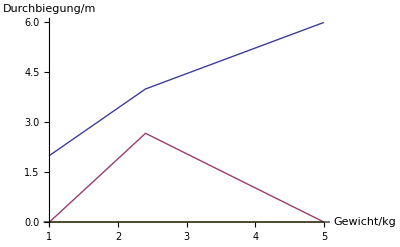

```mathematica
ListLinePlot[{dataAluPlot,dataMesPlot,dataStaPlot},AxesLabel->{"Gewicht/kg","Durchbiegung/m"}]
```

## 4.

### Linear Fit

```mathematica
AluFit=LinearModelFit[dataAluPlot,x,x]
```

FittedModel[1.28155+0.970874 x]

```mathematica
AluFitPara=AluFit["ParameterTableEntries"]
```

{{1.28155,0.547146,2.34225,0.256884},{0.970874,0.16816,5.7735,0.109183}}

```mathematica
MesFit=LinearModelFit[dataMesPlot,x,x]
```

FittedModel[1.25135-0.12945 x]

```mathematica
MesFitPara=MesFit["ParameterTableEntries"]
```

{{1.25135,2.43176,0.514586,0.697448},{-0.12945,0.747379,-0.173205,0.890817}}

```mathematica
StaFit=LinearModelFit[dataStaPlot,x,x]
```

FittedModel[0.+0. x]

```mathematica
StaFitPara=StaFit["ParameterTableEntries"]
```

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

{{0.,0.,ComplexInfinity,0.},{0.,0.,ComplexInfinity,0.}}

### Flächenträgheitsmomente

#### Funktionen

```mathematica
fIAr[{h_,dh_,b_,db_}]:= {(b*h^3)/12,Abs[h^3/12]*db+Abs[(b* h^2)/4]*dh}(*rechteckiger Querschnitt*)
```

```mathematica
fIAk[{d_,dd_}]:={(Pi d^4)/64,Abs[(Pi d^3)/16]dd}(*kreis Querschnitt*)
```

#### Berechnung

```mathematica
dataIAr=Table[{dataStab[[i,1]],dataStabFehler,dataStab[[i,2]],dataStabFehler},{i,2,4}]
```

{{4,1/50,2,1/50},{3,1/50,2,1/50},{0,1/50,0,1/50}}

```mathematica
IAr=Table [fIAr[dataIAr[[i,All]]],{i,1,3}]
```

{{32/3,4/15},{9/2,27/200},{0,0}}

```mathematica
dataIAk = Table[{dataStab[[i,4]],dataStabFehler},{i,2,4}]
```

{{0,1/50},{0,1/50},{1,1/50}}

```mathematica
IAk=Table [fIAk[dataIAk[[i,All]]],{i,1,3}]
```

{{0,0},{0,0},{π/64,π/800}}

### Elastizitätsmodul

```mathematica
fE[{k_,dk_,l_,dl_,IA_,dIA_}]:= {l^3/(48 k IA),Abs[-l^3/(48 IA k^2)]dk+Abs[(3 l^2)/(48 IA k)]dl+Abs[-l^3/(48 k IA^2)]dIA}
```

#### AluStab

```mathematica
dataAluEr={AluFitPara[[2,1]],AluFitPara[[2,2]],dataStab[[2,3]],dataStabFehler,IAr[[1,1]],IAr[[1,2]]}
```

{0.970874,0.16816,10,1/50,32/3,4/15}

```mathematica
dataAluEk={AluFitPara[[2,1]],AluFitPara[[2,2]],dataStab[[2,3]],dataStabFehler,IAk[[1,1]],IAk[[1,2]]}
```

{0.970874,0.16816,10,1/50,0,0}

```mathematica
fE[dataAluEr]
```

{2.01172,0.410803}

```mathematica
fE[dataAluEk]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 ∞ encountered.

{ComplexInfinity,Indeterminate}

#### MessingStab

```mathematica
dataMesEr={MesFitPara[[2,1]],MesFitPara[[2,2]],dataStab[[3,3]],dataStabFehler,IAr[[2,1]],IAr[[2,2]]}
```

{-0.12945,0.747379,40,1/50,9/2,27/200}

```mathematica
dataMesEk={MesFitPara[[2,1]],MesFitPara[[2,2]],dataStab[[3,3]],dataStabFehler,IAk[[2,1]],IAk[[2,2]]}
```

{-0.12945,0.747379,40,1/50,0,0}

```mathematica
fE[dataMesEr]
```

{-2288.89,13287.}

```mathematica
fE[dataMesEk]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 ∞ encountered.

{ComplexInfinity,Indeterminate}

#### Stahlstab

```mathematica
dataStaEk={StaFitPara[[2,1]],StaFitPara[[2,2]],dataStab[[4,3]],dataStabFehler,IAk[[3,1]],IAk[[3,2]]}
```

{0.,0.,23,1/50,π/64,π/800}

```mathematica
dataStaEr={StaFitPara[[2,1]],StaFitPara[[2,2]],dataStab[[4,3]],dataStabFehler,IAr[[3,1]],IAr[[3,2]]}
```

{0.,0.,23,1/50,0,0}

```mathematica
fE[dataStaEr]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0.` ∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 ∞ encountered.

{ComplexInfinity,Indeterminate}

```mathematica
fE[dataStaEk]
```

Power::infy: Infinite expression 1/0.` encountered.

∞::indet: Indeterminate expression 0.` ∞ encountered.

Power::infy: Infinite expression 1/0.` encountered.

General::stop: Further output of Power will be suppressed during this calculation.

{ComplexInfinity,Indeterminate}

## 5.